# Sprott: Bulk Implementation

### Sprott Problem Definitions

These use the top ± definition from Sprott when there is a choice. The ancillary functions and derivatives are defined.  Jump discontinuities are smoothe using tanh(m x) with a default value of m=50.  All problems have parameters {a,b,c,d,m}.  The smoothing parameter is only active in problems 11, 12, and 13.  The functions fSprott[p][y], dyfSprott[p][y] and dpfSprott[p][y] are defined and protected at the bottom of the initialization cell.

```mathematica
Unprotect[Sprott, fSprott];
Sprott=<|
1-><|"fun":>-a y⟦3⟧+b y⟦2⟧-c y+d y⟦2⟧^2,"par"->{2.017,0,1,1,50},"IC"->{0,0,1},"dery":>{-c,b+2 d y⟦2⟧,-a},"derp":>{-y⟦3⟧,y⟦2⟧,-y,y⟦2⟧^2}|>,2-><|"fun":>a y⟦3⟧-b y⟦2⟧+c y⟦1⟧+d y⟦1⟧^2,"par"->{0,2.8,1,1,50},"IC"->{-0.5,-1,1},"dery":>{c+2 d y⟦1⟧,-b,a},"derp":>{y⟦3⟧,-y⟦2⟧,y⟦1⟧,y⟦1⟧^2}|>,3-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧+d (y⟦1⟧^2-1),"par"->{0.44,2,0,1,50},"IC"->{0,0,0},"dery":>{c+2 d y⟦1⟧,-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,-1+y⟦1⟧^2}|>,4-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧+d y⟦1⟧^2,"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"dery":>{c+2 d y⟦1⟧,-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,y⟦1⟧^2}|>,5-><|"fun":>a y⟦3⟧-b y⟦2⟧+c y⟦1⟧+d (Abs[y⟦1⟧]-1),"par"->{0,2,0,1,50},"IC"->{-1,-1,1},"dery":>{c+d Absp[y⟦1⟧],-b,a},"derp":>{y⟦3⟧,-y⟦2⟧,y⟦1⟧,-1+Abs[y⟦1⟧]}|>,6-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧+d (Abs[y⟦1⟧]-1),"par"->{0.6,1,0,1,50},"IC"->{0,0,0},"dery":>{c+d Absp[y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,-1+Abs[y⟦1⟧]}|>,7-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d (Di[y⟦1⟧]-1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0},"dery":>{c-d Dip[y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,1-Di[y⟦1⟧]}|>,8-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d (Rd[y⟦1⟧]+1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0},"dery":>{c-d Rdp[y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,-1-Rd[y⟦1⟧]}|>,9-><|"fun":>a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d (Di[y⟦1⟧]-1),"par"->{0,2.9,0.7,1,50},"IC"->{0,-0.5,0.5},"dery":>{c-d Dip[y⟦1⟧],-b,a},"derp":>{y⟦3⟧,-y⟦2⟧,y⟦1⟧,1-Di[y⟦1⟧]}|>,10-><|"fun":>a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d (Rd[y⟦1⟧]+1),"par"->{0,2.9,0.7,1,50},"IC"->{0,0.5,-0.5},"dery":>{c-d Rdp[y⟦1⟧],-b,a},"derp":>{y⟦3⟧,-y⟦2⟧,y⟦1⟧,-1-Rd[y⟦1⟧]}|>,11-><|"fun":>-a y⟦3⟧-b y⟦2⟧-c y⟦1⟧+d Sg[m][y⟦1⟧],"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+d Sgp[m][y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,-y⟦1⟧,Sg[m][y⟦1⟧]}|>,12-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d Sg[m][y⟦1⟧],"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"dery":>{c-d Sgp[m][y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,-Sg[m][y⟦1⟧]}|>,13-><|"fun":>-a y⟦3⟧-b y⟦2⟧-c y⟦1⟧+d He[m][y⟦1⟧],"par"->{0.7,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+d He[m][y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,-y⟦1⟧,He[m][y⟦1⟧]}|>,14-><|"fun":>-a y⟦3⟧-b y⟦2⟧-c y⟦1⟧+d Sa[y⟦1⟧],"par"->{0.4,1,1,2,50},"IC"->{0,1,0},"dery":>{-c+d Sap[y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,-y⟦1⟧,Sa[y⟦1⟧]}|>,15-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d Sa[y⟦1⟧],"par"->{0.4,1,1,2,50},"IC"->{0,1,0},"dery":>{c-d Sap[y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,-Sa[y⟦1⟧]}|>,16-><|"fun":>-a y⟦3⟧-b y⟦2⟧-c y⟦1⟧+d Tanh[y⟦1⟧],"par"->{0.19,1,1,2,50},"IC"->{0,1,0},"dery":>{-c+d Sech[y⟦1⟧]^2,-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,-y⟦1⟧,Tanh[y⟦1⟧]}|>,17-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d Tanh[y⟦1⟧],"par"->{0.19,1,1,2,50},"IC"->{0,1,0},"dery":>{c-d Sech[y⟦1⟧]^2,-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,-Tanh[y⟦1⟧]}|>,18-><|"fun":>a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d y⟦1⟧^3,"par"->{0,3.7,1,1,50},"IC"->{0,0.5,1},"dery":>{c-3 d y⟦1⟧^2,-b,a},"derp":>{y⟦3⟧,-y⟦2⟧,y⟦1⟧,-y⟦1⟧^3}|>,19-><|"fun":>-a y⟦3⟧+b y⟦2⟧-c y⟦1⟧-d y⟦2⟧^3,"par"->{0.6,2.8,1,1,50},"IC"->{0,1,0},"dery":>{-c,b-3 d y⟦2⟧^2,-a},"derp":>{-y⟦3⟧,y⟦2⟧,-y⟦1⟧,-y⟦2⟧^3}|>,20-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧-d y⟦1⟧^3,"par"->{0.7,1,1,1,50},"IC"->{0,1,0},"dery":>{c-3 d y⟦1⟧^2,-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,-y⟦1⟧^3}|>,21-><|"fun":>-a y⟦3⟧-b y⟦2⟧-c y⟦1⟧+d y⟦1⟧^3,"par"->{0.35,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+3 d y⟦1⟧^2,-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,-y⟦1⟧,y⟦1⟧^3}|>,22-><|"fun":>-a y⟦3⟧-b y⟦2⟧+c y⟦1⟧+d Sin[y⟦1⟧],"par"->{0.2,1,0,1,50},"IC"->{0,1,0},"dery":>{c+d Cos[y⟦1⟧],-b,-a},"derp":>{-y⟦3⟧,-y⟦2⟧,y⟦1⟧,Sin[y⟦1⟧]}|>
|>;
Clear[fSprott]
Quiet[
Do[
fSprott[k,{a_,b_,c_,d_,m_}][y_List]={y⟦2⟧,y⟦3⟧,Sprott[k]["fun"]};
dyfSprott[k,{a_,b_,c_,d_,m_}][y_List]={{0,1,0},{0,0,1},Sprott[k]["dery"]};
fSprott[k][y_List]=fSprott[k,Sprott[k]["par"]][y];
dyfSprott[k][y_List]=dyfSprott[k,Sprott[k]["par"]][y],
{k,22}],
General::partd]
Protect[Sprott, fSprott,dyfSprott];
```

```mathematica
k=4;
y0=Sprott[k]["IC"]
 TMax=123;
ySol=NDSolveValue[{y'[t]==fSprott[k][y[t]],y[0]==y0},y,{t,0, TMax}]
```

{0,1,0}

NDSolveValue::ndsz: At t == 5.38418, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
?NDSolveValue
```

```mathematica
ysol=NDSolveValue[{y''[x]+({{1, 1, 1, 1}, {1, 2, 1, 2}, {1, 1, 3, 1}, {1, 2, 1, 4}}).y[x]==0,y[0]==y'[0]=={1,1,1,1}},y,{x,0,8}]
```

InterpolatingFunction[…]

```mathematica
Unprotect[fSprott]
Clear[fSprott]
k=3;
Quiet[
fSprott[k,{a_,b_,c_,d_,m_}]=Function[y,Evaluate[{y⟦2⟧,y⟦3⟧,Sprott[k]["fun"]}]];
fSprott[k]:=fSprott[k,Sprott[k]["par"]],
General::partd]
```

```mathematica
(* unprotects the functions etc. *)
Unprotect[Sprott,fSprott,dyfSprott,dpfSprott];Clear[Sprott,Di,Dip,Rd,Rdp,Sa,Sap,Sg,Sgp,He,Hep,Absp,a,b,c,d,y,yp,ypp]
Sprott=<|1-><|"fun":>-a ypp+b yp-c y+d yp^2,"par"->{2.017,0,1,1,50},"IC"->{0,0,1},"dery":>{-c,b+2 d yp,-a}|>,2-><|"fun":>a ypp-b yp+c y+d y^2,"par"->{0,2.8,1,1,50},"IC"->{-0.5,-1,1},"dery":>{c+2 d y,-b,a}|>,3-><|"fun":>-a ypp-b yp+c y+d (y^2-1),"par"->{0.44,2,0,1,50},"IC"->{0,0,0},"dery":>{c+2 d y,-b,-a}|>,4-><|"fun":>-a ypp-b yp+c y+d y^2,"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"dery":>{c+2 d y,-b,-a}|>,5-><|"fun":>a ypp-b yp+c y+d (Abs[y]-1),"par"->{0,2,0,1,50},"IC"->{-1,-1,1},"dery":>{c+d Absp[y],-b,a}|>,6-><|"fun":>-a ypp-b yp+c y+d (Abs[y]-1),"par"->{0.6,1,0,1,50},"IC"->{0,0,0},"dery":>{c+d Absp[y],-b,-a}|>,7-><|"fun":>-a ypp-b yp+c y-d (Di[y]-1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0},"dery":>{c-d Dip[y],-b,-a}|>,8-><|"fun":>-a ypp-b yp+c y-d (Rd[y]+1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0},"dery":>{c-d Rdp[y],-b,-a}|>,9-><|"fun":>a ypp-b yp+c y-d (Di[y]-1),"par"->{0,2.9,0.7,1,50},"IC"->{0,-0.5,0.5},"dery":>{c-d Dip[y],-b,a}|>,10-><|"fun":>a ypp-b yp+c y-d (Rd[y]+1),"par"->{0,2.9,0.7,1,50},"IC"->{0,0.5,-0.5},"dery":>{c-d Rdp[y],-b,a}|>,11-><|"fun":>-a ypp-b yp-c y+d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+d Sgp[m][y],-b,-a}|>,12-><|"fun":>-a ypp-b yp+c y-d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"dery":>{c-d Sgp[m][y],-b,-a}|>,13-><|"fun":>-a ypp-b yp-c y+d He[m][y],"par"->{0.7,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+d He[m][y],-b,-a}|>,14-><|"fun":>-a ypp-b yp-c y+d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0},"dery":>{-c+d Sap[y],-b,-a}|>,15-><|"fun":>-a ypp-b yp+c y-d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0},"dery":>{c-d Sap[y],-b,-a}|>,16-><|"fun":>-a ypp-b yp-c y+d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0},"dery":>{-c+d Sech[y]^2,-b,-a}|>,17-><|"fun":>-a ypp-b yp+c y-d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0},"dery":>{c-d Sech[y]^2,-b,-a}|>,18-><|"fun":>a ypp-b yp+c y-d y^3,"par"->{0,3.7,1,1,50},"IC"->{0,0.5,1},"dery":>{c-3 d y^2,-b,a}|>,19-><|"fun":>-a ypp+b yp-c y-d yp^3,"par"->{0.6,2.8,1,1,50},"IC"->{0,1,0},"dery":>{-c,b-3 d yp^2,-a}|>,20-><|"fun":>-a ypp-b yp+c y-d y^3,"par"->{0.7,1,1,1,50},"IC"->{0,1,0},"dery":>{c-3 d y^2,-b,-a}|>,21-><|"fun":>-a ypp-b yp-c y+d y^3,"par"->{0.35,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+3 d y^2,-b,-a}|>,22-><|"fun":>-a ypp-b yp+c y+d Sin[y],"par"->{0.2,1,0,1,50},"IC"->{0,1,0},"dery":>{c+d Cos[y],-b,-a}|>|>;
(* Adding the derivatives wrt to the parameters p={a,b,c} *)
Do[Sprott[k]["derp"]=D[NewSprott[k]["fun"],{{a,b,c,d}}],{k,1,22}]
(* Building easy functions.  The 2nd def overloads the default parameters *)
Clear[fSprott,dyfSprott,dpfSprott]
Do[
fSprott[k,{a_,b_,c_,d_,m_}]=Function[{y,yp,ypp},Evaluate[{yp,ypp,Sprott[k]["fun"]}]];
fSprott[k]=fSprott[k,Sprott[k]["par"]];
dyfSprott[k,{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={{0,1,0},{0,0,1},Sprott[k]["yder"]};
dyfSprott[k][{y_,yp_,ypp_}]=dyfSprott[k,Sprott[k]["par"]][{y,yp,ypp}];
dpfSprott[k,{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]=Sprott[k]["pder"];
dpfSprott[k][{y_,yp_,ypp_}]=dpfSprott[k,Sprott[k]["par"]][{y,yp,ypp}],
{k,1,22}
]
(* Protects the functions etc. *)
Protect[Sprott,fSprott,dyfSprott,dpfSprott];
```

Function::flpar: Parameter specification {{y,yp,ypp}} in Function[{{y,yp,ypp}},{yp,ypp,-c y+b yp+d yp^2-a ypp}] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {{y,yp,ypp}} in Function[{{y,yp,ypp}},{yp,ypp,-y+0 yp+1 yp^2-2.017 ypp}] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {{y,yp,ypp}} in Function[{{y,yp,ypp}},{yp,ypp,c y+d y^2-b yp+a ypp}] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

```mathematica
?Function
```

```mathematica
Unprotect[fSprott]
k=4
fSprott[4,{1,1,1,1,1}][y,yp,ypp]
```

{}

4

{yp,ypp,y+y^2-yp-ypp}

```mathematica
fSprott[4]
```

4

Function[{y,yp,ypp},{yp,ypp,c y+d y^2-b yp-a ypp}]

```mathematica
k=4;
Sprott[k]["fun"]
Function[{y,yp,ypp},Evaluate[{yp,ypp,Sprott[k]["fun"]}]]
```

c y+d y^2-b yp-a ypp

Function[{y,yp,ypp},{yp,ypp,c y+d y^2-b yp-a ypp}]

### ODE Functions

These functions are going to work for more than the Sprott functions

#### Basic Solvers

I built f, dyf and dpf (assumed linear dependence) for the Sprott problems.  I want to solve our different sensitivity problems (only the y needs an initial condition) and return interpolating functions!  Following the discussion we want to be able to choose TMax.

```mathematica
ODERun[f_,y0_,TMax_]:=NDSolveValue[{y'[t]==f[y[t]],y[0]==y0},
y,{t,0,TMax}]
ODERun[{f_,dyf_},y0_,TMax_]:=NDSolveValue[{
y'[t]==f[y[t]],y[0]==y0,
J'[t]==dyf[y[t]].J[t],J[0]=IdentityMatrix[Length[y0]]},
{y,J},{t,0,TMax}]
ODERun[{f_,dyf_,dpf_},y0_,TMax_]:=NDSolveValue[{
y'[t]==f[y[t]],y[0]==y0,
J'[t]==dyf[y[t]].J[t],J[0]=IdentityMatrix[Length[y0]],
p'[t]==dpf[y[t]]+dyf[y[t]].p'[t], p[0]==ConstantArray[0.0,Length[dpf[y0]]]},
{y,J,p},{t,0,TMax}]
```

```mathematica
fSprott[4,{0.5,1,1,1,50}][{1,2,3}]
```

fSprott[4,{0.5,1,1,1,50}][{1,2,3}]

```mathematica
NDSolveValue[{y'[t]==fSprott[4][y[t]],y[0]==y0},y,{t,0, TMax}]
```

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolveValue[{y'[t]==fSprott[4,{0.5,1,1,1,50}][y[t]],y[0]=={0,1,0}},y,{t,0,123}]

```mathematica
TMax=123;
k=4;
y0=Sprott[k]["IC"]
fSprott[k]
ODERun[fSprott[k,Sprott[k]["par"]],y0,TMax]
```

{0,1,0}

fSprott[4,{0.5,1,1,1,50}]

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolveValue[{y'[t]==fSprott[4,{0.5,1,1,1,50}][y[t]],y[0]=={0,1,0}},y,{t,0,123}]

```mathematica
Sim
```

These use the top ± definition from Sprott when there is a choice. The ancillary functions and derivatives are defined.  Jump discontinuities are smoothe using tanh(m x) with a default value of m=50.  All problems have parameters {a,b,c,d,m}.  The smoothing parameter is only active in problems 11, 12, and 13.  The functions fSprott[p][y], dyfSprott[p][y] and dpfSprott[p][y] are defined and protected at the bottom of the initialization cell.

Here are a bunch of useful functions

I put them in an association rather than a list.  The delayed assignment :> means the right hand side is not evaluated until called. An association means you can call things out by name.  This matches up directly with dictionaries in Julia, Python, and MATLAB.   All also have some type of lower level “struct” construction.

I added definitions of the derivatives of all the functions (and their derivatives) beside where they were defined.  Mma was doing most (maybe all) of the derivatives correctly.  I changed the variables to {y,yp,ypp}.

Request for Equilibrium Solver.   We need to think about what we are going to do with the parameters

Request for y and J solver.  I am added the derivative of the defining function wrt {y,yp,ypp} to the structure.

### Equilibrium Problem

Thinking about the equilibrium problem.   We need to know what to do with the parameters.

```mathematica
k=5;
NewSprott[k]["fun"]/.{yp->0,ypp->0}
```

c y+d (-1+Abs[y])

```mathematica
TableForm[Table[
SprottProb=NewSprott[k];
Solve[SprottProb["fun"]==0/.{yp->0,ypp->0},y],
{k,1,22}],TableHeadings->Automatic]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

General::stop: Further output of Solve::nsmet will be suppressed during this calculation.

| 1 | 2 | 3
1 | y→0 |  | 
2 | y→0 | y→-c/d | 
3 | y→(-c-√(c^2+4 d^2))/(2 d) | y→(-c+√(c^2+4 d^2))/(2 d) | 
4 | y→0 | y→-c/d | 
5 | y→d/(c-d) | y→d/(c+d) | 
6 | y→d/(c-d) | y→d/(c+d) | 
7 |  |  | 
8 |  |  | 
9 |  |  | 
10 |  |  | 
11 | Solve[-c y+d Tanh[m y]==0,y] |  | 
12 | Solve[c y-d Tanh[m y]==0,y] |  | 
13 | Solve[-c y+1/2 d (1+Tanh[m y])==0,y] |  | 
14 | y→0 |  | 
15 | y→0 |  | 
16 | Solve[-c y+d Tanh[y]==0,y] |  | 
17 | Solve[c y-d Tanh[y]==0,y] |  | 
18 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
19 | y→0 |  | 
20 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
21 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
22 | Solve[c y+d Sin[y]==0,y] |  |

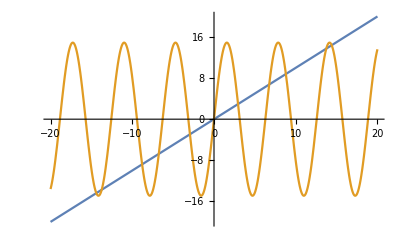

```mathematica
dOverc = 14.9;
Plot[ { y, dOverc Sin[y]},{y, -20,20}]
```

```mathematica
Clear[c,d]
k=7
Sprott[k]["fun"]/.{yp->0,ypp->0}
c=d=1
Plot[Sprott[7]["fun"]/.{yp->0,ypp->0},{y,-2,2}]
```

7

c y-d (-1+Max[0,y])

1

### Basic yJ Solver

Thinking about the basic solver.   We need to know what to do with the parameters.  In some ways this is much easier than the equilibrium computation.  We will always have values for the parameters.  The first thing I would do is build and example out of one of the problems

```mathematica
Clear[a,b,c,d,m]
k=8;
Clear[f, df]
f[{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={yp,ypp,NewSprott[k]["fun"]};
df[{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={{0,1,0},{0,0,1},NewSprott[k]["der"]};
p=NewSprott[k]["par"];
f[p][{y,yp,ypp}];
u0=NewSprott[k]["IC"];
TMax=123;
{uSol,JSol}=NDSolveValue[{u'[t]==f[p][u[t]],J'[t]==df[p][u[t]].J[t],u[0]==u0,J[0]==IdentityMatrix[3]},{u,J},{t,0, TMax}];
ParametricPlot3D[uSol[t],{t,0, TMax},PlotRange->All]
JSol[1]
SingularValueList[JSol[TMax],Tolerance->0]
```

-Graphics3D-

{{0.848717,0.915866,0.435116},{-0.434958,0.718094,0.785331},{-0.785234,-0.670715,0.482495}}

{943.144,3.62149,8.59873×10^-15}

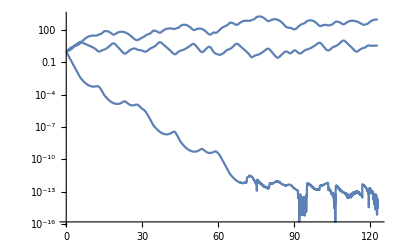

```mathematica
LogPlot[ SingularValueList[JSol[t],Tolerance->0], {t, 0, TMax}]
```

```mathematica
TableForm[Table[
SprottProb=NewSprott[k];
Solve[SprottProb["fun"]==0/.{yp->0,ypp->0},y],
{k,1,22}],TableHeadings->Automatic]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

General::stop: Further output of Solve::nsmet will be suppressed during this calculation.

| 1 | 2 | 3
1 | y→0 |  | 
2 | y→0 | y→-c/d | 
3 | y→(-c-√(c^2+4 d^2))/(2 d) | y→(-c+√(c^2+4 d^2))/(2 d) | 
4 | y→0 | y→-c/d | 
5 | y→d/(c-d) | y→d/(c+d) | 
6 | y→d/(c-d) | y→d/(c+d) | 
7 |  |  | 
8 |  |  | 
9 |  |  | 
10 |  |  | 
11 | Solve[-c y+d Tanh[m y]==0,y] |  | 
12 | Solve[c y-d Tanh[m y]==0,y] |  | 
13 | Solve[-c y+1/2 d (1+Tanh[m y])==0,y] |  | 
14 | y→0 |  | 
15 | y→0 |  | 
16 | Solve[-c y+d Tanh[y]==0,y] |  | 
17 | Solve[c y-d Tanh[y]==0,y] |  | 
18 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
19 | y→0 |  | 
20 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
21 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
22 | Solve[c y+d Sin[y]==0,y] |  |

```mathematica
{c,d}={1,1};Plot[ ]
```

1

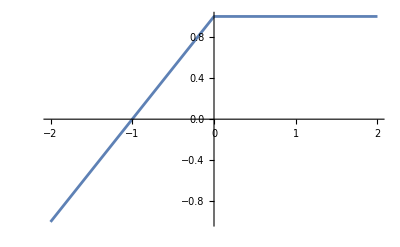

```mathematica
Clear[c,d]
c=d=1
Plot[Sprott[7]["fun"]/.{yp->0,ypp->0},{y,-2,2}]
```

R

```mathematica
k=6;
Sprott[k]
```

<|fun:>-a ypp-b yp+c y+d (Abs[y]-1),par→{0.6,1,0,1,50},IC→{0,0,0}|>

What else do I need to define? What functions do I want?